```mathematica
$MaxPrecision = 42
(*
eps = e-2, e-6, e-17

[0; 1]

Begin
R1:=Exp((Degree(x,4)+2*Degree(x,3)-5*x+6)/5);
R2:=Coh(1/(-15*Degree(x,3)+10*x+5*Sqrt(10)));
VarF:=R1+R2-3;
End;
*)
```

42

```mathematica
(*Метод дихотомии*)
F[x_]:=Exp[(x^4+2 * x^3 - 5*x+6)]+
Cosh[1/(-15*x^3+10*x+5*Sqrt[10])]-3;
Dexot[precision_]:=Module[{graphValues, NonGraphValues},
eps = 10^-precision;
delta = eps/5;
leftBound = 0;
rightBound = 1;
nextLeftBound[a_, b_]:=(a+b)/2-delta;
nextRightBound[a_, b_]:=(a+b)/2+delta;
IterationCountrer = 0;
intervals= List[];
AppendTo[intervals, {leftBound,rightBound}];

graphValues=List[];
NonGraphValues=List[];
While[(rightBound -leftBound) > eps,
nextLeft = nextLeftBound[leftBound, rightBound];
nextRight = nextRightBound[leftBound, rightBound];
leftFunc = F[nextLeft];
rightFunc = F[nextRight];
If[leftFunc <= rightFunc,
rightBound=nextRight;
AppendTo[graphValues, {rightBound, rightFunc}];
AppendTo[NonGraphValues, {nextLeft, leftFunc}];
,
leftBound = nextLeft;
AppendTo[graphValues, {nextLeft, leftFunc}];
AppendTo[NonGraphValues, {rightBound, rightFunc}];
] ;
AppendTo[intervals, {leftBound,rightBound}];
++IterationCountrer;
];
If[Length[intervals]>80,
temp = List[];
For[i = 1, i < Length[intervals], i+=2,
AppendTo[temp, intervals[[i]]];
];
intervals = temp;
];
(*Subscript[x, min]=SetPrecision[(rightBound+leftBound)/2,20];
Subscript[y, min]=SetPrecision[F[Subscript[x, min]],20];
*)
Subscript[x, min]=N[(rightBound+leftBound)/2];
Subscript[y, min]=N[F[Subscript[x, min]]];
Print["Answer: ",NumberForm[Subscript[y, min],{25, precision}],"\nIterations: ", IterationCountrer, "\nFunction calculations: ", IterationCountrer * 2, "\nPrecition: ", precision, "\nx_min = ",Subscript[x, min] ];
(*Return[SetPrecision[N[F[rightBound-leftBound]],20]];*)
Print[Show[
DiscretePlot[intervals[[k]], {k, 1,Length[intervals]}, AxesLabel->{iteration, interval}, GridLines->Automatic], Graphics[Table[Line[{{k, intervals[[k]][[1]]},{k, intervals[[k]][[2]]}}], {k, 1, Length[intervals]}]]]];
Return[
Show[Plot[F[x], {x, 0.4, 1.1}, PlotRange->{{0.4, 1.1},{0,80}}],
ListPlot[{{Subscript[x, min], Subscript[y, min]}}, PlotStyle->{Black},PlotLegends->{"minimum"} ],
AxesLabel->{"x","y"}
]
];
];
(*
ListPlot[{ graphValues,NonGraphValues},PlotStyle->{Red, Green},PlotLegends->{"included in calculations","excluded from calculations"}],
*)
```

```mathematica
(*Метод дихотомииб результаты*)
```

Answer: 28.27
Iterations: 8
Function calculations: 16
Precition: 2
x_min = 0.747055

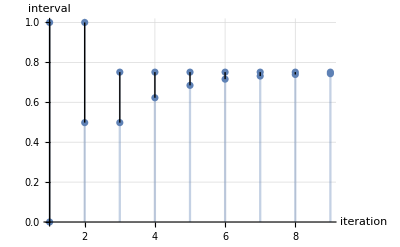

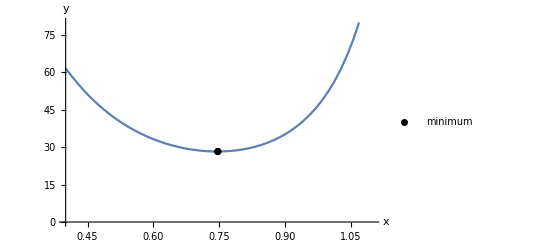

```mathematica
(*Погрешность 0.01*)
Dexot[2]
```

Answer: 28.267932
Iterations: 21
Function calculations: 42
Precition: 6
x_min = 0.74601

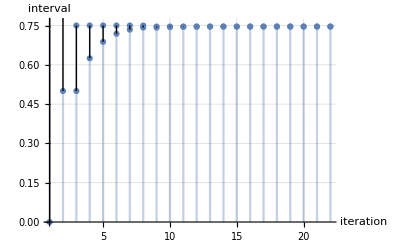

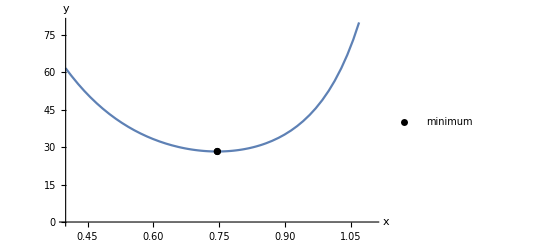

```mathematica
(*Погрешность 10^-6*)
Dexot[6]
```

Answer: 28.26793230872697000
Iterations: 58
Function calculations: 116
Precition: 17
x_min = 0.74601

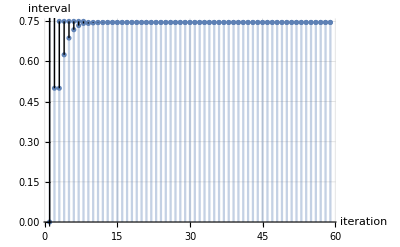

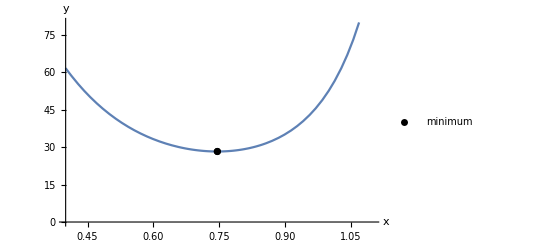

```mathematica
(*Погрешность 10^-17*)
Dexot[17]
```

```mathematica
Abort[]
```

$Aborted

```mathematica
(*Метод золотого сечения*)
 
GoldenRat[precision_]:=Module[{},
AccuracyGoal-> precision;
eps = 10^-precision;
leftBound = 0;
rightBound = 1;
intervals=List[];
goldenRat = (1+Sqrt[5])/2;
nextLeftBound[a_, b_]:= a+(1-1/goldenRat)(b-a);
nextRightBound[a_, b_]:= a +(b-a)/goldenRat;
(*nextLeftBound[a_, b_]:= a+(b-a)/(goldenRat+1);
nextRightBound[a_, b_]:= b-(b-a)/(goldenRat+1);*)
AppendTo[intervals, {leftBound,rightBound}];
nextLeft=nextLeftBound[leftBound, rightBound];

nextRight=nextRightBound[leftBound, rightBound];
leftFunc = F[leftBound];
rightFunc = F[rightBound];
IterationCountrer=1;

While[(rightBound-leftBound) > eps,
If[leftFunc > rightFunc,
leftBound = nextLeft;
nextLeft=nextRight;
leftFunc=rightFunc;
(*nextRight = leftBound + rightBound  - nextLeft;*)
nextRight= nextRightBound[leftBound, rightBound];
rightFunc=F[nextRight];
,
rightBound = nextRight;
nextRight=nextLeft;
rightFunc=leftFunc;
(*nextLeft = leftBound + rightBound  - nextRight;*)
nextLeft= nextLeftBound[leftBound, rightBound];
leftFunc=F[nextLeft];
];
AppendTo[intervals, {leftBound,rightBound}];
++IterationCountrer;
];
(*Subscript[x, min]=SetPrecision[(rightBound+leftBound)/2,20];
Subscript[y, min]=SetPrecision[F[Subscript[x, min]],20];
*)
Subscript[x, min]=N[(rightBound+leftBound)/2];
Subscript[y, min]=N[F[Subscript[x, min]]];
Print["Answer: ",NumberForm[Subscript[y, min],{25, precision}],"\nIterations: ", IterationCountrer, "\nFunction calculations: ", IterationCountrer +1, "\nPrecition: ", precision, "\nx_min = ",Subscript[x, min] ];

Print[Show[
DiscretePlot[intervals[[k]], {k, 1, Length[intervals]}, AxesLabel->{iteration, interval}, GridLines->Automatic], Graphics[Table[Line[{{k, intervals[[k]][[1]]},{k, intervals[[k]][[2]]}}], {k, 1, Length[intervals]}]]]];

Print[Show[Plot[F[x], {x, 0.4, 1.1}, PlotRange->{{0.4, 1.1},{0,80}}],
ListPlot[{{Subscript[x, min], Subscript[y, min]}}, PlotStyle->{Black},PlotLegends->{"minimum"} ],
AxesLabel->{"x","y"}
]];
Return[Subscript[y, min]];
];
```

Answer: 28.27
Iterations: 11
Function calculations: 12
Precition: 2
x_min = 0.746711

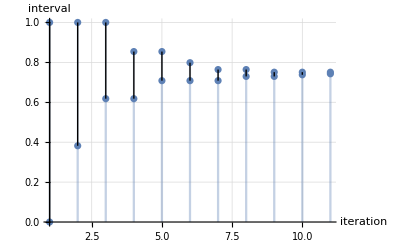

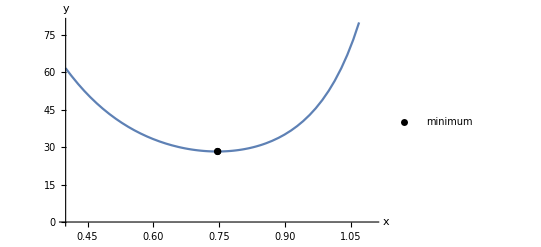

```mathematica
(*Метод золотого сечения, результаты*)
(*Погрешность 0.01*)
GoldenRat[2];
```

Answer: 28.267932
Iterations: 30
Function calculations: 31
Precition: 6
x_min = 0.74601

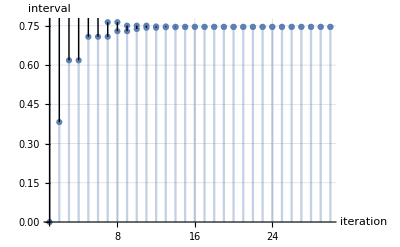

-Graphics-

```mathematica
(*Погрешность 10^-6*)
GoldenRat[6];
```

Answer: 52.60243075173498000
Iterations: 83
Function calculations: 84
Precition: 17
x_min = 1.

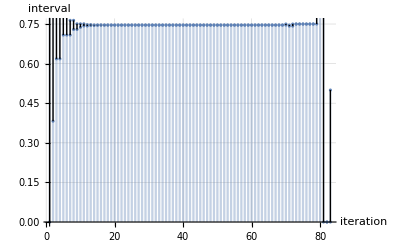

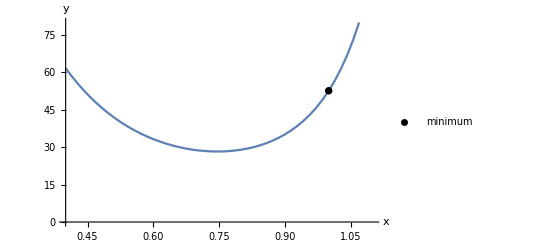

```mathematica
(*Погрешность 10^-17*)
GoldenRat[17];
```

```mathematica
(*
Вывод

Ни один из методов не дает точный ответ, так как результат получается сравнением значений функции в конечном числе точек.

Из результатов работы программ следует, что метод золотого сечения эффективнее, чем метод дихотомии. Совершается меньше вычислений функций и итераций. Теоретический материал учебника "Введение в методы оптимизации" (А.В.Аттеков и др.) подтверждает это.
*)
```

```mathematica
NumberForm[FindMinimum[F[x], {x, 0, 1}],{25, 18}]
```

{28.267932308726960000,{x→0.746010224026561400}}